# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Poincare

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];


Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],200];
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
(*randomregion=Table[{i,0},{i,0,1.9990,0.001}];*)
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=-randomregion;
randomregion//Length
```

200

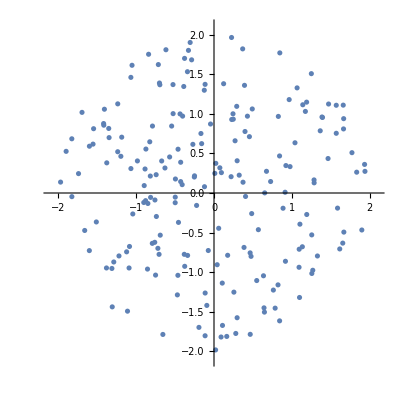

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
k=15.;
θ=-α/2;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
poincarea
```

-Graphics-

```mathematica
Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]];
```

```mathematica
Export["poincare_zoom_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{0.9,1.1},{0.4,0.6}}]];
```

```mathematica
(*Define the map and its Jacobian*)standardMap[{x_,y_},K_]:=Module[{yn,xn},yn=y+K Sin[x];
xn=Mod[x+yn,2 Pi];
{xn,yn}];

jacobianStandardMap[{x_,y_},K_]:=Module[{dx,dy},dx=1+K Cos[x];
dy=1;
{{dx,dy},{1,1}}];

(*Compute the FTLE*)
Clear[computeFTLE];
computeFTLE[map_,jacobian_,grid_,nSteps_,K_]:=Module[{ftleValues,trajectory,jacobianTrajectory,cumulativeJacobian,singularValues,lambda},(*FTLE computation for each grid point*)ftleValues=ParallelTable[Module[{z0={x,y},z,J,Jcum,singularValueMax},(*Initialize cumulative Jacobian*)Jcum=IdentityMatrix[2];
z=z0;
(*Iterate map and Jacobian*)
Do[J=jacobian[z,K];
Jcum=J.Jcum;(*Accumulate Jacobian product*)z=map[z,K];,{n,1,nSteps}];
(*Compute the largest singular value*)singularValueMax=Max[SingularValueList[Jcum]];
(*FTLE calculation*)lambda=Log[singularValueMax]/nSteps;
lambda],{x,grid[[1,1]],grid[[1,2]],grid[[1,3]]},{y,grid[[2,1]],grid[[2,2]],grid[[2,3]]}];
ftleValues];
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=8.0; (*Parameter for standard map*)
nSteps=2; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=2.0; (*Parameter for standard map*)
nSteps=10; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic]
```

-Graphics-

```mathematica
kicks=20000;
k=20.;
θ=-α/2;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
selectedPoints=Select[newpoincarea,(0.9<=#[[1]]<=1.1)&&(0.4<=#[[2]]<=0.6)&];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[selectedPoints]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
selectedPoints=Select[newpoincarea,(0.9<=#[[1]]<=1.1)&&(0.4<=#[[2]]<=0.6)&];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[selectedPoints]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Export["poincare_zoom_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{0.9,1.1},{0.4,0.6}}]];
```

## Lyapunov

## Definiciones

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];

Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=mapeo[Qini,α,k,n]=Module[{a,list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=mapeob[Qini,α,k,n]=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

Clear[MDpf,MDpb];
MDpf[Qini_,n_,d_]:=Module[{orbit=mapeo[Qini,α,k,n]},
Total[Table[((Abs[orbit[[i+1]][[1]]-orbit[[i]][[1]]])^d+(Abs[orbit[[i+1]][[2]]-orbit[[i+1]][[2]]])^d),{i,1,n}]]
];

MDpb[Qini_,n_,d_]:=Module[{orbit=mapeob[Qini,α,k,n]},
Total[Table[((Abs[orbit[[i+1]][[1]]-orbit[[i]][[1]]])^d+(Abs[orbit[[i+1]][[2]]-orbit[[i+1]][[2]]])^d),{i,1,n}]]
];

Clear[rec];
(*usando norma infinito*)
rec[i_,j_]:=Module[{a=Norm[data[[i]]-data[[j]],Infinity]},
If[a<=ϵ,1,0]
];
(*rec[qi_,α_,k_,n_]:=Module[{data=mapeo2[qi,α,k,n]},
Table[If[Norm[data[[i]]-data[[j]],Infinity]<=ϵ,1,0],{i,1,Length[data]},{j,1,Length[data]}]
];*)
(*rec[qi_,α_,k_,n_]:=Module[{data=mapeo2[qi,α,k,n]},
SparseArray[{{i_,j_}/;Norm[data[[i]]-data[[j]],Infinity]<=ϵ->1},{n+1,n+1}]
];*)
```

```mathematica
Clear[jmas2];
jmas2[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[2,2]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];

Clear[jmas3];
jmas3[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[3,3]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];
(*jmas[Jini_,A_Real,n_Integer]:=Module[{j,list=mapeoJ[N[Jini],N[A],n],data,B=N[Pi/2]},
data=Table[N[M[list[[i]],N[A],N[B]]],{i,1,n}];
j=N[Log[Max[N[Abs[N[Eigenvalues[N[Fold[Dot,data]]]]]]]^(N[1/n])]]
];*)
```

## Lyapunov

```mathematica
Clear[mapeo1,jmas];
mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];

(*jmas[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[1,1]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];*)

jmas[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s={},lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[1,1]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];
```

## Method

```mathematica
{q0,p0}=RandomPoint[Disk[{0,0},1.999],1][[1]]
```

{-0.392831,-0.809362}

```mathematica
s0=change2[{q0,p0}]
```

{-0.350844,-0.722853,-0.595309}

```mathematica
α=0.84;
k=20.;
```

```mathematica
nlist=Range[100];
```

```mathematica
serie=jmas[s0,α,k,1000];
```

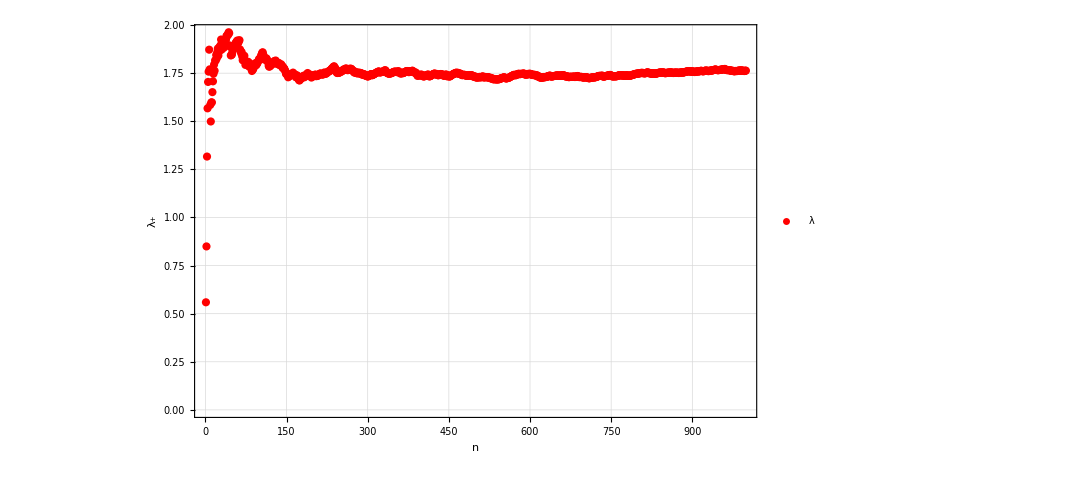

```mathematica
plot1=ListPlot[serie,PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Red,PlotLegends->{Style["λ",20,Black]}]
```

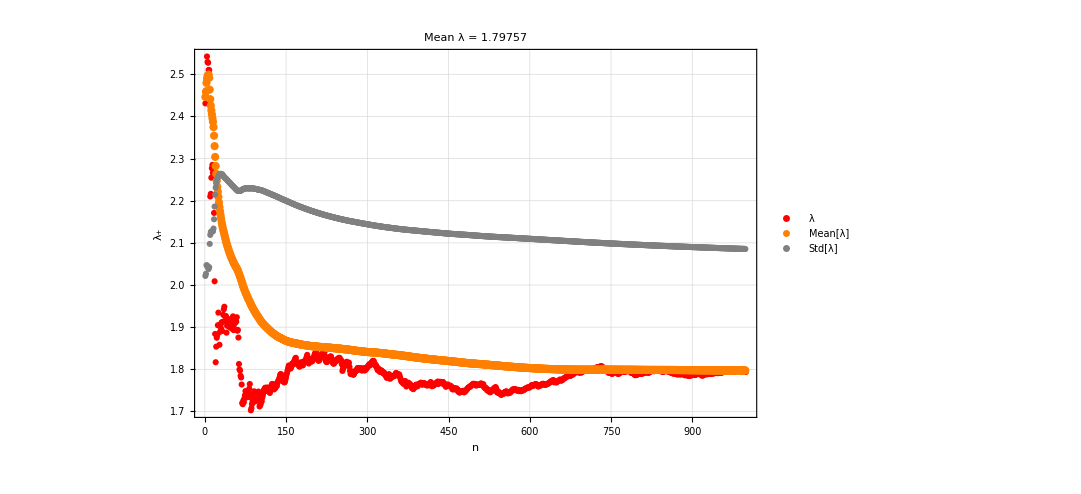

```mathematica
mean={};
std={};
Do[
data1=serie[[1;;i]];
AppendTo[mean,Mean[data1]];
AppendTo[std,StandardDeviation[data1]];
,{i,2,Length[serie]}];
plot2=ListPlot[mean,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Orange,PlotLegends->{Style["Mean[λ]",20,Black]}];
plot3=ListPlot[std+2,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Gray,PlotLegends->{Style["Std[λ]",20,Black]}];
Show[plot1,plot2,plot3,PlotRange->All,PlotLabel->Style["Mean λ = "<>ToString[Mean[mean[[-100;;-1]]]],30]]
```

## Quantum initial conditions

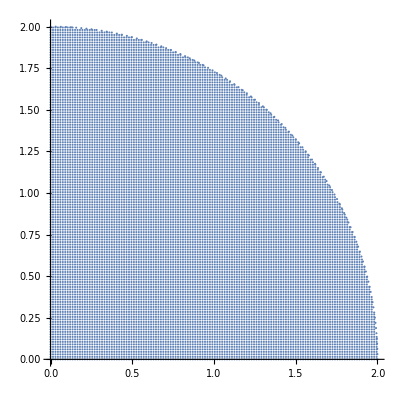

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
regions=Table[change2[i],{i,region}];
```

```mathematica
serie=ParallelTable[jmas[i,α,k,1000],{i,regions}];
```

```mathematica
lyapunovs=Table[{region[[i,1]],region[[i,2]],Mean[serie[[i]][[1;;10]]]},{i,Length[region]}];
```

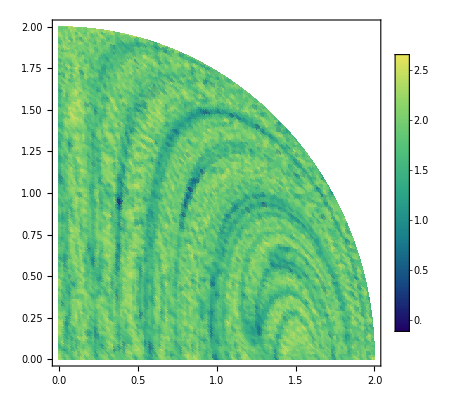

```mathematica
ListDensityPlot[lyapunovs,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow"]
```

```mathematica
lyapunovs=Table[{region[[i,1]],region[[i,2]],Mean[serie[[i]][[-200;;-1]]]},{i,Length[region]}];
```

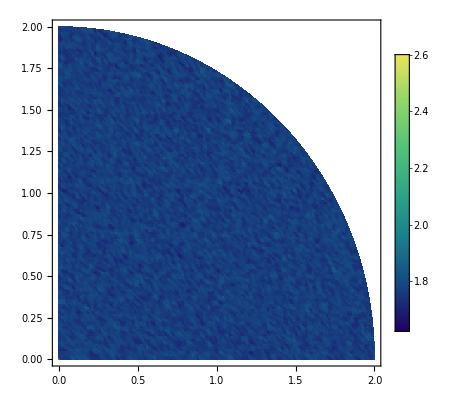

```mathematica
ListDensityPlot[lyapunovs,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow"]
```

```mathematica
Export["lyapunov.png",a,ImageSize->1000]
```

lyapunov.png

```mathematica
region//Length
```

14202

```mathematica
regionPoints=Select[region,(0.9<=#[[1]]<=1.1)&&(0.4<=#[[2]]<=0.6)&];
```

```mathematica
regionIndices=Flatten[Quiet[Position[region,_?(Function[p,0.9<=p[[1]]<=1.1&&0.4<=p[[2]]<=0.6])]]]
```

{7889,7890,7891,7892,7893,7894,7895,7896,7897,7898,7899,7900,7901,7902,8009,8010,8011,8012,8013,8014,8015,8016,8017,8018,8019,8020,8021,8022,8128,8129,8130,8131,8132,8133,8134,8135,8136,8137,8138,8139,8140,8141,8247,8248,8249,8250,8251,8252,8253,8254,8255,8256,8257,8258,8259,8260,8365,8366,8367,8368,8369,8370,8371,8372,8373,8374,8375,8376,8377,8378,8482,8483,8484,8485,8486,8487,8488,8489,8490,8491,8492,8493,8494,8495,8599,8600,8601,8602,8603,8604,8605,8606,8607,8608,8609,8610,8611,8612,8715,8716,8717,8718,8719,8720,8721,8722,8723,8724,8725,8726,8727,8728,8831,8832,8833,8834,8835,8836,8837,8838,8839,8840,8841,8842,8843,8844,8946,8947,8948,8949,8950,8951,8952,8953,8954,8955,8956,8957,8958,8959,9061,9062,9063,9064,9065,9066,9067,9068,9069,9070,9071,9072,9073,9074,9175,9176,9177,9178,9179,9180,9181,9182,9183,9184,9185,9186,9187,9188,9288,9289,9290,9291,9292,9293,9294,9295,9296,9297,9298,9299,9300,9301,9401,9402,9403,9404,9405,9406,9407,9408,9409,9410,9411,9412,9413,9414}

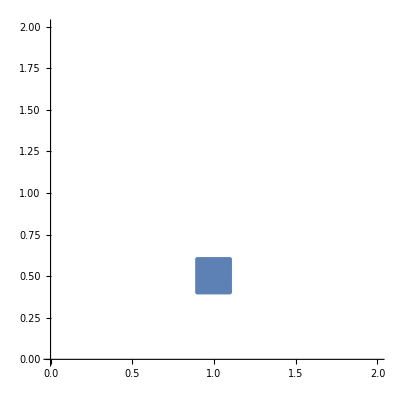

```mathematica
ListPlot[Table[region[[i]],{i,regionIndices}],AspectRatio->1,PlotRange->{{0,2},{0,2}}]
```

```mathematica
regionIndices//Length
```

196

```mathematica
serie//Length
```

14202

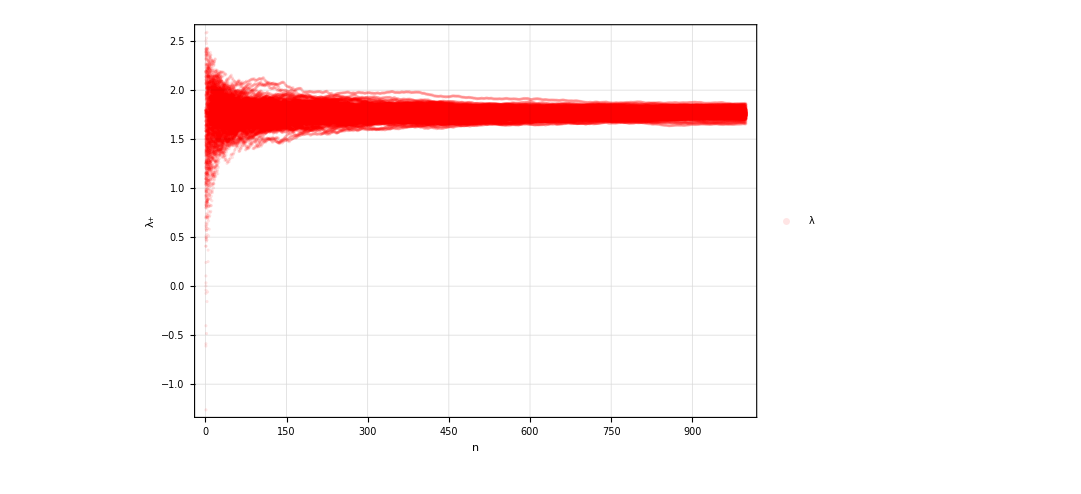

```mathematica
ListPlot[Table[serie[[i]],{i,regionIndices}],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.1]],PlotLegends->{Style["λ",20,Black]}]
```

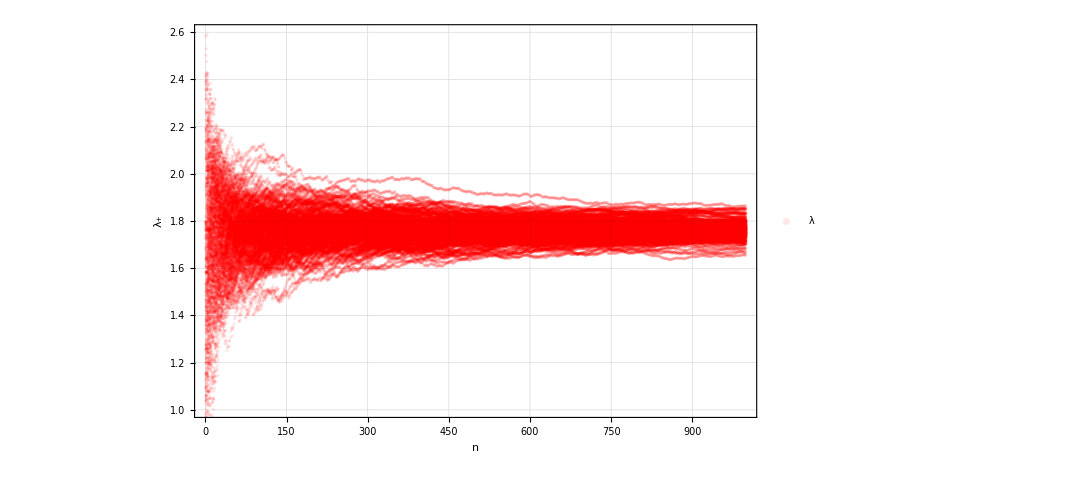

```mathematica
plota=ListPlot[Table[serie[[i]],{i,regionIndices}],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.1]],PlotLegends->{Style["λ",20,Black]}]
```

```mathematica
plots=Table[ListPlot[serie[[regionIndices[[i]]]],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[1]],PlotLegends->{Style["λ",20,Black]}],{i,1,Length[regionIndices]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
regionIndices=Flatten[Quiet[Position[region,_?(Function[p,1.2<=p[[1]]<=1.4&&1.1<=p[[2]]<=1.3])]]]
```

{10218,10219,10220,10221,10222,10223,10224,10225,10226,10227,10228,10229,10230,10325,10326,10327,10328,10329,10330,10331,10332,10333,10334,10335,10336,10337,10431,10432,10433,10434,10435,10436,10437,10438,10439,10440,10441,10442,10443,10537,10538,10539,10540,10541,10542,10543,10544,10545,10546,10547,10548,10549,10642,10643,10644,10645,10646,10647,10648,10649,10650,10651,10652,10653,10654,10746,10747,10748,10749,10750,10751,10752,10753,10754,10755,10756,10757,10758,10849,10850,10851,10852,10853,10854,10855,10856,10857,10858,10859,10860,10861,10951,10952,10953,10954,10955,10956,10957,10958,10959,10960,10961,10962,10963,11053,11054,11055,11056,11057,11058,11059,11060,11061,11062,11063,11064,11065,11154,11155,11156,11157,11158,11159,11160,11161,11162,11163,11164,11165,11166,11254,11255,11256,11257,11258,11259,11260,11261,11262,11263,11264,11265,11266,11353,11354,11355,11356,11357,11358,11359,11360,11361,11362,11363,11364,11365,11451,11452,11453,11454,11455,11456,11457,11458,11459,11460,11461,11462,11463,11548,11549,11550,11551,11552,11553,11554,11555,11556,11557,11558,11559,11560}

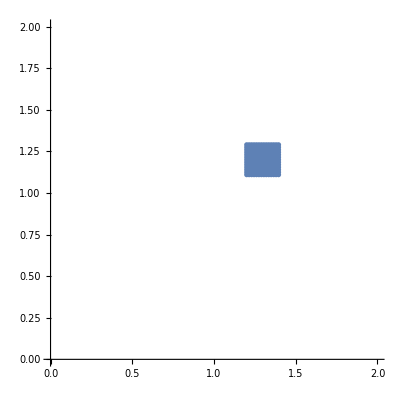

```mathematica
ListPlot[Table[region[[i]],{i,regionIndices}],AspectRatio->1,PlotRange->{{0,2},{0,2}}]
```

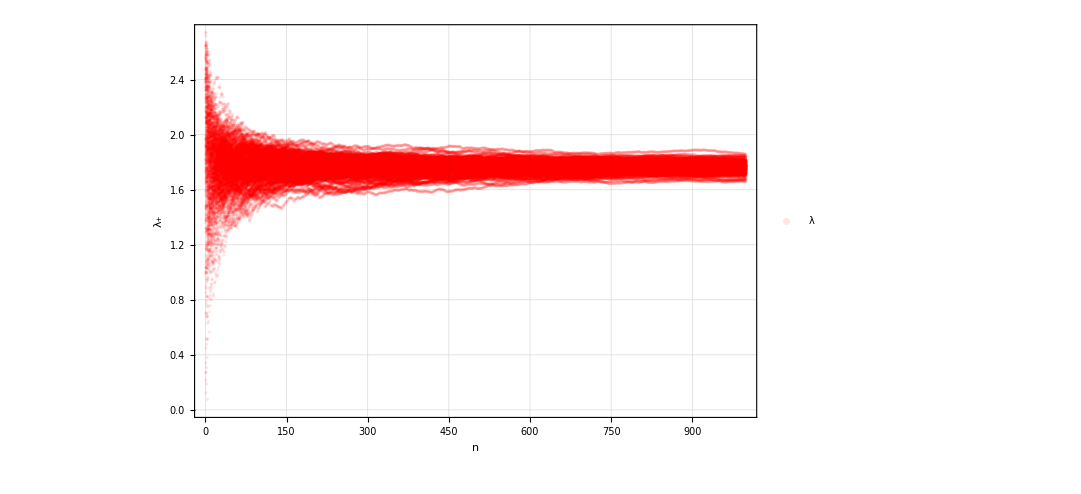

```mathematica
ListPlot[Table[serie[[i]],{i,regionIndices}],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.1]],PlotLegends->{Style["λ",20,Black]}]
```

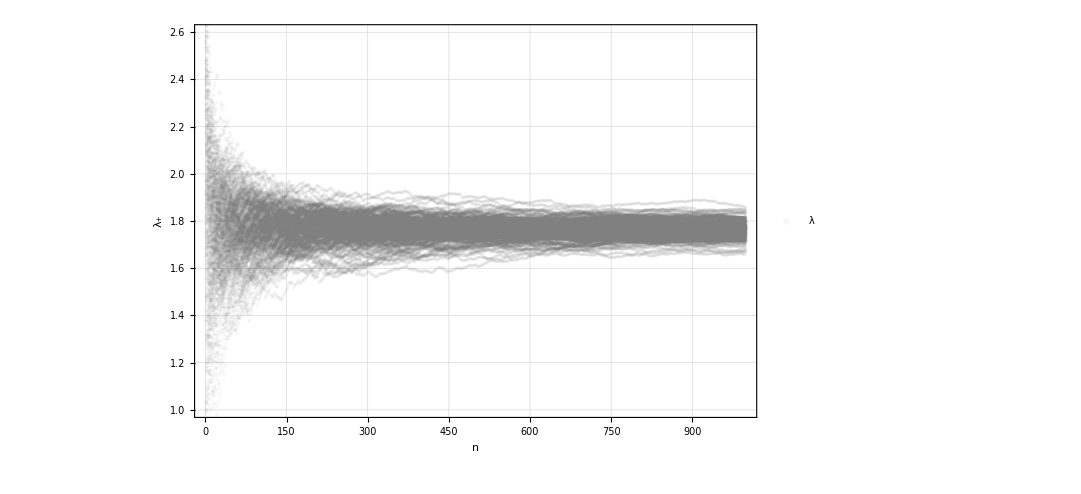

```mathematica
plotb=ListPlot[Table[serie[[i]],{i,regionIndices}],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Gray,Opacity[0.05]],PlotLegends->{Style["λ",20,Black]}]
```

```mathematica
plots=Table[ListPlot[serie[[regionIndices[[i]]]],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[1]],PlotLegends->{Style["λ",20,Black]}],{i,1,Length[regionIndices]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
Show[plota,plotb]
```

-Graphics-

## Other initial conditions

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

-Graphics-

```mathematica
regions=Table[change2[i],{i,randomregion}];
```

```mathematica
serie=ParallelTable[jmas[i,α,k,1000],{i,regions}];
```

```mathematica
serie//Dimensions
```

{2000,999}

```mathematica
ListPlot[Table[serie[[i]],{i,1,100}],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.1]],PlotLegends->{Style["λ",20,Black]}]
```

-Graphics-

## Real sphere

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[mapeo3];
mapeo3[sini_,α_,k_,n_]:=Module[{list},
list=NestList[Fun[α,k,#]&,sini,n]
];
```

```mathematica
Fun[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s];
mapeo4[sini_,α_,k_,n_,p_]:=Module[{list},
list=NestList[Fun[α,k,#,p]&,sini,n]];
```

```mathematica
randompoints=RandomPoint[Sphere[],10];
```

```mathematica
α=0.84;
```

```mathematica
ListPointPlot3D[randompoints,BoxRatios->{1, 1, 1},PlotTheme->"Detailed",ViewPoint->{2,-2,2},AxesLabel->{"X","Y","Z"},Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
n=2000;
k=20.;
p=5000;
trayectories=ParallelTable[mapeo4[i,α,k,n,p],{i,randompoints}];
```

```mathematica
ListPointPlot3D[Flatten[trayectories,1],BoxRatios->{1, 1, 1},PlotRange->All,PlotTheme->"Detailed",ViewPoint->{1,-2,2},AxesLabel->{"X","Y","Z"},Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
radius=1.99999;
delta=0.2;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;
randomregion//Length
```

508

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

-Graphics-

```mathematica
randomregion2=Map[change2[#]&,randomregion];
```

```mathematica
ListPointPlot3D[randomregion2,BoxRatios->{1, 1, 1},PlotRange->All,PlotTheme->"Detailed",ViewPoint->{1,-2,2},AxesLabel->{"X","Y","Z"},Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
n=1500;
k=12.;
p=5000;
trayectories=ParallelTable[mapeo4[i,α,k,n,p],{i,randomregion2}];
```

```mathematica
ListPointPlot3D[Flatten[trayectories,1],BoxRatios->{1, 1, 1},PlotRange->All,PlotTheme->"Detailed",ViewPoint->{1,-2,2},AxesLabel->{"X","Y","Z"},Boxed->False,ImageSize->600]
```

-Graphics3D-

## Powers of Poincaré

```mathematica
Clear[F,Fun];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];
Clear[mapeo];
mapeo[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=Pi/2;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],200];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=-randomregion;
randomregion//Length
```

200

```mathematica
radius=1.99999;
delta=0.05;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
randomregion=circlePoints;
randomregion//Length
```

5015

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

-Graphics-

```mathematica
kicks=500;
k=11.6;
p=1;
```

```mathematica
plist={1,2,100,1000};
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks,p]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.02],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>".png",poincarec];

,{p,plist}]
```

Join::normal: Nonatomic expression expected at position 1 in Join[IterationLimit].

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[Join[IterationLimit],{10055571,2}].

$Aborted

## Cycle for plotting

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks,p]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.01],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",poincarec];

,{k,klist}];
```

```mathematica
Show[poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

## Eigenvalues analysis

```mathematica
Clear[F];
F[α_,k_,s_,p_]:=Module[{a,sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p]
];
```

```mathematica
α=0.84;
k=20;
```

```mathematica
radius=1.99999;
delta=0.2;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
circlePoints=Select[gridPoints,Norm[#]<radius&];
randomregion=circlePoints;
randomregion//Length
```

307

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

-Graphics-

```mathematica
s0=Table[change2[i],{i,randomregion}];
```

```mathematica
α=0.84;
k=20.;
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[F[α,k,s0[[10]],2]]]]]
```

{{-0.124852-0.992175 ⅈ,-0.124852+0.992175 ⅈ,1.},{{-0.00557794-0.700823 ⅈ,0.705862+0. ⅈ,0.0415591-0.0940624 ⅈ},{-0.00557794+0.700823 ⅈ,0.705862+0. ⅈ,0.0415591+0.0940624 ⅈ},{-0.13279+0. ⅈ,-0.0593004+0. ⅈ,0.989369+0. ⅈ}}}

```mathematica
Det[F[α,k,s0[[1]],2]]
```

1.

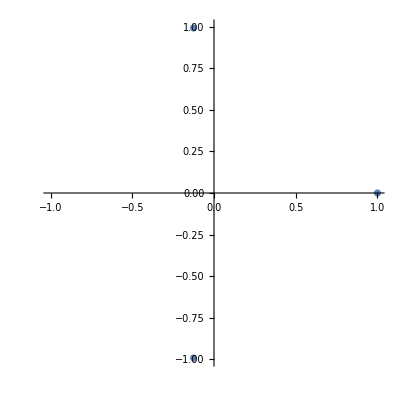

```mathematica
ComplexListPlot[eigenval,PlotRange->{{-1,1},{-1,1}}]
```